# Check of the Fs

## Check of F0:

We have:
B=  γ_E+ln(2) -(ⅈ π)/2
α = -γ_E-ln(2) +2
then the relations between B and α are: 
B = -α-(ⅈ π)/2 + 2   and α= -B-(ⅈ π)/2 + 2.

Let’s find  F0 both written with respect to B and α:

```mathematica
FullSimplify[∫_x^∞ ⅇ^(2ⅈ u)/u ⅆu, Assumptions-> x>0]
```

Gamma[0,-2 ⅈ x]

F0 = Gamma[0,-2 ⅈ x] = ∫_x^∞ ⅇ^(2ⅈ u)/u ⅆu expressed with B = γ_E+ln(2) -(ⅈ π)/2

```mathematica
FullSimplify[Normal[Series[Gamma[0,-2 ⅈ x],{x,0,1}]]/.EulerGamma->+(ⅈ π)/2+B-Log[2],Assumptions->x>0]//Expand
```

-B-2 ⅈ x-Log[x]

```mathematica
FullSimplify[Normal[Series[Gamma[0,-2 ⅈ x],{x,0,1}]]/.EulerGamma->2-α-Log[2],Assumptions->x>0]//Expand
```

-2+(ⅈ π)/2-2 ⅈ x+α-Log[x]

## Check of F1:

```mathematica
FullSimplify[∫_x^∞ ⅇ^(+2ⅈ u)/u Log[u]ⅆu, Assumptions-> x>0]
```

2 ⅈ x HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ x]+1/24 (12 EulerGamma^2-12 ⅈ EulerGamma π-π^2+12 Log[2]^2+12 ⅈ π Log[x/2])+EulerGamma Log[2 x]+1/2 Log[x] (-2 ExpIntegralEi[2 ⅈ x]+Log[4 x])

```mathematica
FullSimplify[Normal[Series[2 ⅈ x HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ x]+1/24 (12 EulerGamma^2-12 ⅈ EulerGamma π-π^2+12 Log[2]^2+12 ⅈ π Log[x/2])+EulerGamma Log[2 x]+1/2 Log[x] (-2 ExpIntegralEi[2 ⅈ x]+Log[4 x]),{x,0,1}]]/.EulerGamma->+(ⅈ π)/2+B-Log[2],Assumptions->x>0]//Expand
```

B^2/2+π^2/12+2 ⅈ x-2 ⅈ x Log[x]-Log[x]^2/2

```mathematica
(B^2/2+π^2/12+2 ⅈ x-2 ⅈ x Log[x]-Log[x]^2/2) /. B-> -α-(ⅈ π)/2+2 //Expand
```

2-ⅈ π-π^2/24+2 ⅈ x-2 α+(ⅈ π α)/2+α^2/2-2 ⅈ x Log[x]-Log[x]^2/2

## Check of F2:

We have:
B=  γ_E+ln(2) -(ⅈ π)/2
α = -γ_E-ln(2) +2
then the relations between B and α are: 
B = -α-(ⅈ π)/2 + 2   and α = -B-(ⅈ π)/2 + 2.

```mathematica
FullSimplify[∫_x^∞ ⅇ^(+2ⅈ u)/u Log[u]^2 ⅆu, Assumptions-> x>0]
```

1/24 (-8 EulerGamma^3+ⅈ π^3-96 ⅈ x HypergeometricPFQ[{1,1,1,1},{2,2,2,2},2 ⅈ x]+12 ⅈ EulerGamma^2 (π+2 ⅈ Log[2])+12 ⅈ π Log[2]^2+2 EulerGamma (π^2+12 ⅈ π Log[2]-12 Log[2]^2)+π^2 Log[4]+4 Log[x] (24 ⅈ x HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ x]+Log[x] (6 EulerGamma+3 ⅈ π-6 ExpIntegralEi[2 ⅈ x]+Log[64]+4 Log[x]))-8 (Log[2]^3+2 Zeta[3]))

```mathematica
FullSimplify[Normal[Series[1/24 (-8 EulerGamma^3+ⅈ π^3-96 ⅈ x HypergeometricPFQ[{1,1,1,1},{2,2,2,2},2 ⅈ x]+12 ⅈ EulerGamma^2 (π+2 ⅈ Log[2])+12 ⅈ π Log[2]^2+2 EulerGamma (π^2+12 ⅈ π Log[2]-12 Log[2]^2)+π^2 Log[4]+4 Log[x] (24 ⅈ x HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ x]+Log[x] (6 EulerGamma+3 ⅈ π-6 ExpIntegralEi[2 ⅈ x]+Log[64]+4 Log[x]))-8 (Log[2]^3+2 Zeta[3])),{x,0,1}]]/.EulerGamma->+(ⅈ π)/2+B-Log[2],Assumptions->x>0]//Expand
```

-B^3/3-(B π^2)/6-4 ⅈ x+4 ⅈ x Log[x]-2 ⅈ x Log[x]^2-Log[x]^3/3-(2 Zeta[3])/3

```mathematica
(-B^3/3-(B π^2)/6-4 ⅈ x+4 ⅈ x Log[x]-2 ⅈ x Log[x]^2-Log[x]^3/3-(2 Zeta[3])/3) /.  B-> -α-(ⅈ π)/2+2 //Expand
```

-8/3+2 ⅈ π+π^2/6+(ⅈ π^3)/24-4 ⅈ x+4 α-2 ⅈ π α-(π^2 α)/12-2 α^2+1/2 ⅈ π α^2+α^3/3+4 ⅈ x Log[x]-2 ⅈ x Log[x]^2-Log[x]^3/3-(2 Zeta[3])/3

## Check of F00:

Let’s find an expression for F00 = ∫_x^∞ ⅇ^(-2ⅈ u)/u(∫_u^∞ ⅇ^(2ⅈ t)/t ⅆt)ⅆu

The integrand is:

```mathematica
FullSimplify[ⅇ^(-2ⅈ u)/u(-2+(ⅈ π)/2+α-Log[u]),Assumptions->x>0]//Expand
```

-(2 ⅇ^(-2 ⅈ u))/u+(ⅈ ⅇ^(-2 ⅈ u) π)/(2 u)+(ⅇ^(-2 ⅈ u) α)/u-(ⅇ^(-2 ⅈ u) Log[u])/u

Then we integrate:

```mathematica
FullSimplify[Integrate[-(2 ⅇ^(-2 ⅈ u))/u+(ⅈ ⅇ^(-2 ⅈ u) π)/(2 u)+(ⅇ^(-2 ⅈ u) α)/u-(ⅇ^(-2 ⅈ u) Log[u])/u,{u, x,+∞}]/.EulerGamma->2-α-Log[2], Assumptions-> x>0]
```

1/24 (-12 EulerGamma^2+π (7 π-12 ⅈ (-2+α))+48 ⅈ x HypergeometricPFQ[{1,1,1},{2,2,2},-2 ⅈ x]-12 ⅈ π Log[2]-12 Log[2]^2-12 ⅈ EulerGamma (π-ⅈ Log[4])-12 Log[x] (2 EulerGamma+Log[4]+Log[x])+12 CosIntegral[2 x] (4-ⅈ π-2 α+2 Log[x])-12 (4 ⅈ+π-2 ⅈ α+2 ⅈ Log[x]) SinIntegral[2 x])

```mathematica
FullSimplify[Normal[Series[1/24 (-12 EulerGamma^2+π (7 π-12 ⅈ (-2+α))+48 ⅈ x HypergeometricPFQ[{1,1,1},{2,2,2},-2 ⅈ x]-12 ⅈ π Log[2]-12 Log[2]^2-12 ⅈ EulerGamma (π-ⅈ Log[4])-12 Log[x] (2 EulerGamma+Log[4]+Log[x])+12 CosIntegral[2 x] (4-ⅈ π-2 α+2 Log[x])-12 (4 ⅈ+π-2 ⅈ α+2 ⅈ Log[x]) SinIntegral[2 x]),{x,0,1}]]/.EulerGamma->2-α-Log[2],Assumptions->x>0]//Expand
```

2-ⅈ π+(7 π^2)/24-2 ⅈ x-π x-2 α+(ⅈ π α)/2+2 ⅈ x α+α^2/2+2 Log[x]-1/2 ⅈ π Log[x]-2 ⅈ x Log[x]-α Log[x]+Log[x]^2/2

This solution is slightly different from the one fnd by Mario:

```mathematica
FullSimplify[(2-ⅈ π+(7 π^2)/24-2 ⅈ x-π x-2 α+(ⅈ π α)/2+2 ⅈ x α+α^2/2+2 Log[x]-1/2 ⅈ π Log[x]-2 ⅈ x Log[x]-α Log[x]+Log[x]^2/2) -(2-ⅈ π+π^2/8-π x-2 α+(ⅈ π α)/2+2 ⅈ x α+α^2/2+2 Log[x]-1/2 ⅈ π Log[x]-2 ⅈ x Log[x]-α Log[x]+Log[x]^2/2)]
```

π^2/6-2 ⅈ x

## Another kind of check for F00

```mathematica
FullSimplify[ⅇ^(-2ⅈ u)/u(Gamma[0,-2 ⅈ u]),Assumptions->x>0]//Expand
```

(ⅇ^(-2 ⅈ u) Gamma[0,-2 ⅈ u])/u

```mathematica
FullSimplify[Integrate[(ⅇ^(-2 ⅈ u) Gamma[0,-2 ⅈ u])/u,{u, x,+∞}]/.EulerGamma->2-α-Log[2], Assumptions-> x>0]
```

1/8 (3 π^2-4 ⅈ π (-2+α)-4 (-2+α)^2+4 (4-ⅈ π-2 α) ExpIntegralEi[-2 ⅈ x]+32 ⅈ x HypergeometricPFQ[{1,1,1},{2,2,2},-2 ⅈ x]+8 (-2+α) Log[x]-4 Log[x] (-2 CosIntegral[2 x]+Log[x]+2 ⅈ SinIntegral[2 x])-4 Hypergeometric1F1^(2,0,0)[0,1,-2 ⅈ x])

```mathematica
FullSimplify[Normal[Series[1/8 (3 π^2-4 ⅈ π (-2+α)-4 (-2+α)^2+4 (4-ⅈ π-2 α) ExpIntegralEi[-2 ⅈ x]+32 ⅈ x HypergeometricPFQ[{1,1,1},{2,2,2},-2 ⅈ x]+8 (-2+α) Log[x]-4 Log[x] (-2 CosIntegral[2 x]+Log[x]+2 ⅈ SinIntegral[2 x])-4 Derivative[2,0,0][Hypergeometric1F1][0,1,-2 ⅈ x]),{x,0,1}]]  /.EulerGamma->2-α-Log[2],Assumptions->x>0]//Expand
```

2-ⅈ π+π^2/8-π x-2 α+(ⅈ π α)/2+2 ⅈ x α+α^2/2+2 Log[x]-1/2 ⅈ π Log[x]-2 ⅈ x Log[x]-α Log[x]+Log[x]^2/2-1/2 Hypergeometric1F1^(2,0,0)[0,1,0]+ⅈ x Hypergeometric1F1^(2,0,1)[0,1,0]

```mathematica
N[-1/2 Derivative[2,0,0][Hypergeometric1F1][0,1,0]+ⅈ x Derivative[2,0,1][Hypergeometric1F1][0,1,0]]
```

0.+0. ⅈ

Then:
2-ⅈ π+π^2/8-π x-2 α+(ⅈ π α)/2+2 ⅈ x α+α^2/2+2 Log[x]-1/2 ⅈ π Log[x]-2 ⅈ x Log[x]-α Log[x]+Log[x]^2/2

In total agreement with the result find by Mario: 
∫_x^∞ ⅇ^(-2 ⅈ u)/u(∫_u^∞ ⅇ^(2 ⅈ t)/t ⅆt)ⅆu = (EulerGamma+Log[2 I x]+Gamma[0,2 ⅈ x])*Gamma[0,-2 ⅈ x]+1/2*(Zeta[2]+(EulerGamma+Log[-2 I x])^2)+ⅇ^(2 ⅈ x)∑_(m=0)^∞ ((∑_(n=0)^m ((-2 I x)^n/Factorial[n]))/(m+1)^2)+∑_(k=1)^∞ ((2 I x)^k/(k^2 Factorial[k])) ≃ 2-ⅈ π+π^2/8-π x-2 α+(ⅈ π α)/2+2 ⅈ x α+α^2/2+2 Log[x]-1/2 ⅈ π Log[x]-2 ⅈ x Log[x]-α Log[x]+Log[x]^2/2 ;

Let’s switch from α to B, and then we find F00 as expressed by 2205.12608:

```mathematica
(2-ⅈ π+π^2/8-π x-2 α+(ⅈ π α)/2+2 ⅈ x α+α^2/2+2 Log[x]-1/2 ⅈ π Log[x]-2 ⅈ x Log[x]-α Log[x]+Log[x]^2/2) /.α-> -B - (ⅈ π)/2+2 //Expand
```

B^2/2+π^2/4+4 ⅈ x-2 ⅈ B x+B Log[x]-2 ⅈ x Log[x]+Log[x]^2/2

## Check of F10:

```mathematica
∫_x^∞ ⅇ^(-2ⅈ u)/u Log[u](∫_u^∞ ⅇ^(2ⅈ t)/t ⅆt)ⅆu
```

```mathematica
FullSimplify[Normal[Series[ⅇ^(-2ⅈ u)/u Log[u](Gamma[0,-2 ⅈ u]),{u,0,2}]] /. EulerGamma->-α-ln(2)+2 ,Assumptions->u>0]//Expand
```

2 ⅈ Log[u]+π Log[u]-(2 Log[u])/u+(ⅈ π Log[u])/(2 u)-2 ⅈ α Log[u]+(α Log[u])/u+2 ⅈ Log[u]^2-Log[u]^2/u

```mathematica
FullSimplify[∫_x^1 (2 ⅈ Log[u]+π Log[u]-(2 Log[u])/u+(ⅈ π Log[u])/(2 u)-2 ⅈ α Log[u]+(α Log[u])/u+2 ⅈ Log[u]^2-Log[u]^2/u)ⅆu, Assumptions-> x>0]//Expand
```

ConditionalExpression[2 ⅈ-π-2 ⅈ x+π x+2 ⅈ α-2 ⅈ x α+2 ⅈ x Log[x]-π x Log[x]+2 ⅈ x α Log[x]+Log[x]^2-1/4 ⅈ π Log[x]^2-2 ⅈ x Log[x]^2-1/2 α Log[x]^2+Log[x]^3/3,x≠1]

Here we plot the full and the approximated integrands in order to understand if our approximation works.

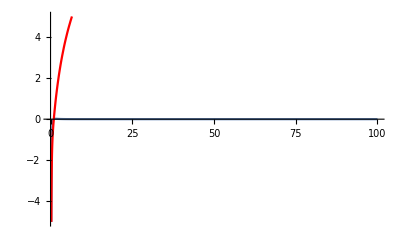

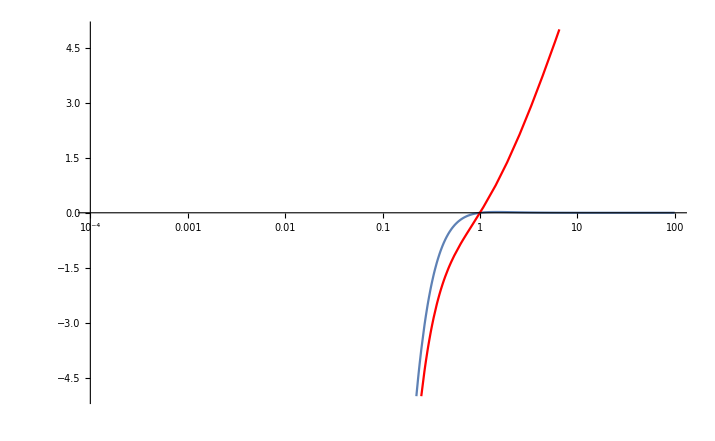

```mathematica
g[x_] := Re[ⅇ^(-2ⅈ x)/x Log[x](Gamma[0,-2 ⅈ x])];
gg[x_] := Re[2 ⅈ Log[x]+π Log[x]-(2 Log[x])/x+(ⅈ π Log[x])/(2 x)-2 ⅈ α Log[x]+(α Log[x])/x+2 ⅈ Log[x]^2-Log[x]^2/x] ;
plot1 = Plot[g[x],{x,0.0001,100}, PlotRange->{-5,5}];
plot2 = Plot[gg[x],{x,0.0001,100}, PlotStyle->Red, PlotRange->{-5,5}];
logplot1 = LogLinearPlot[g[x],{x,0.0001,100}, PlotRange->{-5,5}];
logplot2 = LogLinearPlot[gg[x],{x,0.0001,100}, PlotStyle->Red, PlotRange->{-5,5}];
Show[plot1,plot2]
Show[logplot1,logplot2]
```

## Check of F01:

```mathematica
∫_x^∞ ⅇ^(-2ⅈ u)/u(∫_u^∞ ⅇ^(2ⅈ t)/t Log[t]ⅆt)ⅆu
```

Integrating by parts it is possible to found: 

∫_x^∞ ⅇ^(-2ⅈ u)/u(∫_u^∞ ⅇ^(2ⅈ t)/t Log[t]ⅆt)ⅆu=∫_x^∞ ⅇ^(-2ⅈ u)/u ⅆu*∫_x^∞ ⅇ^(2ⅈ v)/v Log[v]ⅆv-∫_x^∞ ⅇ^(2ⅈ u)/u Log[u](∫_u^∞ ⅇ^(-2ⅈ t)/t ⅆt)ⅆu

This equation corresponds to the equation (same equation of B3 in 2205.12608)
F01  = \bar{F}0 F1 - \bar{F}10
then:

```mathematica
barF0lim = -2-(ⅈ π)/2+2 ⅈ x+α-Log[x]; 
F1lim = 2-ⅈ π-π^2/24+2 ⅈ x-2 α+(ⅈ π α)/2+α^2/2-2 ⅈ x Log[x]-Log[x]^2/2; 
barF10lim = -2 ⅈ-π+2 ⅈ x+π x-2 ⅈ α+2 ⅈ x α-2 ⅈ x Log[x]-π x Log[x]-2 ⅈ x α Log[x]+Log[x]^2+1/4 ⅈ π Log[x]^2+2 ⅈ x Log[x]^2-1/2 α Log[x]^2+Log[x]^3/3;
```

```mathematica
barF0timesF1 = FullSimplify[( -2-(ⅈ π)/2+2 ⅈ x+α-Log[x])( 2-ⅈ π-π^2/24+2 ⅈ x-2 α+(ⅈ π α)/2+α^2/2-2 ⅈ x Log[x]-Log[x]^2/2)]//Expand
```

-4+ⅈ π-(5 π^2)/12+(ⅈ π^3)/48+3 π x-1/12 ⅈ π^2 x-4 x^2+6 α-ⅈ π α+(5 π^2 α)/24-2 ⅈ x α-π x α-3 α^2+1/4 ⅈ π α^2+ⅈ x α^2+α^3/2-2 Log[x]+ⅈ π Log[x]+1/24 π^2 Log[x]+2 ⅈ x Log[x]-π x Log[x]+4 x^2 Log[x]+2 α Log[x]-1/2 ⅈ π α Log[x]-2 ⅈ x α Log[x]-1/2 α^2 Log[x]+Log[x]^2+1/4 ⅈ π Log[x]^2+ⅈ x Log[x]^2-1/2 α Log[x]^2+Log[x]^3/2

Then we obtain F01 as

```mathematica
FullSimplify[(-4+ⅈ π-(5 π^2)/12+(ⅈ π^3)/48+3 π x-1/12 ⅈ π^2 x-4 x^2+6 α-ⅈ π α+(5 π^2 α)/24-2 ⅈ x α-π x α-3 α^2+1/4 ⅈ π α^2+ⅈ x α^2+α^3/2-2 Log[x]+ⅈ π Log[x]+1/24 π^2 Log[x]+2 ⅈ x Log[x]-π x Log[x]+4 x^2 Log[x]+2 α Log[x]-1/2 ⅈ π α Log[x]-2 ⅈ x α Log[x]-1/2 α^2 Log[x]+Log[x]^2+1/4 ⅈ π Log[x]^2+ⅈ x Log[x]^2-1/2 α Log[x]^2+Log[x]^3/2)-(-2 ⅈ-π+2 ⅈ x+π x-2 ⅈ α+2 ⅈ x α-2 ⅈ x Log[x]-π x Log[x]-2 ⅈ x α Log[x]+Log[x]^2+1/4 ⅈ π Log[x]^2+2 ⅈ x Log[x]^2-1/2 α Log[x]^2+Log[x]^3/3)]//Expand
```

(-4+2 ⅈ)+(1+ⅈ) π-(5 π^2)/12+(ⅈ π^3)/48-2 ⅈ x+2 π x-1/12 ⅈ π^2 x-4 x^2+(6+2 ⅈ) α-ⅈ π α+(5 π^2 α)/24-4 ⅈ x α-π x α-3 α^2+1/4 ⅈ π α^2+ⅈ x α^2+α^3/2-2 Log[x]+ⅈ π Log[x]+1/24 π^2 Log[x]+4 ⅈ x Log[x]+4 x^2 Log[x]+2 α Log[x]-1/2 ⅈ π α Log[x]-1/2 α^2 Log[x]-ⅈ x Log[x]^2+Log[x]^3/6

## Check of F000:

F000 = ∫_x^∞ ⅇ^(2ⅈ u)/u(∫_u^∞ ⅇ^(-2ⅈ t)/t(∫_t^∞ ⅇ^(2ⅈ s)/s ⅆs)ⅆt)ⅆu).

```mathematica
F00= 1/8 (3 π^2-4 ⅈ π (-2+α)-4 (-2+α)^2+4 (4-ⅈ π-2 α) ExpIntegralEi[-2 ⅈ x]+32 ⅈ x HypergeometricPFQ[{1,1,1},{2,2,2},-2 ⅈ x]+8 (-2+α) Log[x]-4 Log[x] (-2 CosIntegral[2 x]+Log[x]+2 ⅈ SinIntegral[2 x])-4 Derivative[2,0,0][Hypergeometric1F1][0,1,-2 ⅈ x]); 
F00lim = (B^2/2+π^2/4+4 ⅈ u-2 ⅈ B u+B Log[u]-2 ⅈ u Log[u]+Log[u]^2/2)
```

```mathematica
FullSimplify[Integrate[ⅇ^(2ⅈ u)/u(1/8 (3 π^2-4 ⅈ π (-2+α)-4 (-2+α)^2+4 (4-ⅈ π-2 α) ExpIntegralEi[-2 ⅈ u]+32 ⅈ u HypergeometricPFQ[{1,1,1},{2,2,2},-2 ⅈ u]+8 (-2+α) Log[u]-4 Log[u] (-2 CosIntegral[2 u]+Log[u]+2 ⅈ SinIntegral[2 u])-4 Derivative[2,0,0][Hypergeometric1F1][0,1,-2 ⅈ u])),{u, x,1}]/.EulerGamma->2-α-Log[2], Assumptions-> x>0, Assumptions-> u>0]//Expand
```

∫_x^1 1/(8 u)ⅇ^(2 ⅈ u) (3 π^2-4 ⅈ π (-2+α)-4 (-2+α)^2+4 (4-ⅈ π-2 α) ExpIntegralEi[-2 ⅈ u]+32 ⅈ u HypergeometricPFQ[{1,1,1},{2,2,2},-2 ⅈ u]+8 (-2+α) Log[u]-4 Log[u] (-2 CosIntegral[2 u]+Log[u]+2 ⅈ SinIntegral[2 u])-4 Hypergeometric1F1^(2,0,0)[0,1,-2 ⅈ u])ⅆu

Mathematica is not able to perform the integration, neither if we set the upper bound of the integral as 1 instead of +∞. Then, we choose to keep the limit form of F00:

```mathematica
FullSimplify[Integrate[ⅇ^(2ⅈ u)/u(B^2/2+π^2/4+B Log[u]+Log[u]^2/2),{u, x,+∞}]/.EulerGamma->2-α-Log[2], Assumptions-> x>0, Assumptions-> u>0]//Expand
```

(B EulerGamma^2)/2-EulerGamma^3/6+1/4 ⅈ B^2 π-1/2 ⅈ B EulerGamma π+1/4 ⅈ EulerGamma^2 π-(B π^2)/24+(EulerGamma π^2)/24+(7 ⅈ π^3)/48-1/2 B^2 CosIntegral[2 x]-1/4 π^2 CosIntegral[2 x]+2 ⅈ B x HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ x]-2 ⅈ x HypergeometricPFQ[{1,1,1,1},{2,2,2,2},2 ⅈ x]-1/2 EulerGamma^2 Log[2]-1/2 ⅈ B π Log[2]+1/2 ⅈ EulerGamma π Log[2]-Log[2]^3/6+1/48 π^2 Log[4]+1/6 B Log[2] Log[8]-1/6 EulerGamma Log[2] Log[8]+1/12 ⅈ π Log[2] Log[8]-B CosIntegral[2 x] Log[x]+2 ⅈ x HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ x] Log[x]+1/4 B Log[16] Log[x]+1/2 B Log[x]^2+1/2 EulerGamma Log[x]^2-1/2 CosIntegral[2 x] Log[x]^2+1/12 Log[64] Log[x]^2+Log[x]^3/3+B EulerGamma Log[2 x]-1/2 ⅈ B^2 SinIntegral[2 x]-1/4 ⅈ π^2 SinIntegral[2 x]-ⅈ B Log[x] SinIntegral[2 x]-1/2 ⅈ Log[x]^2 SinIntegral[2 x]-Zeta[3]/3

```mathematica
FullSimplify[Normal[Series[(B EulerGamma^2)/2-EulerGamma^3/6+1/4 ⅈ B^2 π-1/2 ⅈ B EulerGamma π+1/4 ⅈ EulerGamma^2 π-(B π^2)/24+(EulerGamma π^2)/24+(7 ⅈ π^3)/48-1/2 B^2 CosIntegral[2 x]-1/4 π^2 CosIntegral[2 x]+2 ⅈ B x HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ x]-2 ⅈ x HypergeometricPFQ[{1,1,1,1},{2,2,2,2},2 ⅈ x]-1/2 EulerGamma^2 Log[2]-1/2 ⅈ B π Log[2]+1/2 ⅈ EulerGamma π Log[2]-Log[2]^3/6+1/48 π^2 Log[4]+1/6 B Log[2] Log[8]-1/6 EulerGamma Log[2] Log[8]+1/12 ⅈ π Log[2] Log[8]-B CosIntegral[2 x] Log[x]+2 ⅈ x HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ x] Log[x]+1/4 B Log[16] Log[x]+1/2 B Log[x]^2+1/2 EulerGamma Log[x]^2-1/2 CosIntegral[2 x] Log[x]^2+1/12 Log[64] Log[x]^2+Log[x]^3/3+B EulerGamma Log[2 x]-1/2 ⅈ B^2 SinIntegral[2 x]-1/4 ⅈ π^2 SinIntegral[2 x]-ⅈ B Log[x] SinIntegral[2 x]-1/2 ⅈ Log[x]^2 SinIntegral[2 x]-Zeta[3]/3,{x,0,0}]]  /.EulerGamma->+(ⅈ π)/2+B-Log[2],Assumptions->x>0]//Expand
```

-B^3/6-(B π^2)/4-1/2 B^2 Log[x]-1/4 π^2 Log[x]-1/2 B Log[x]^2-Log[x]^3/6-Zeta[3]/3

We now plot F00 to understand if our approximation was worth or not.

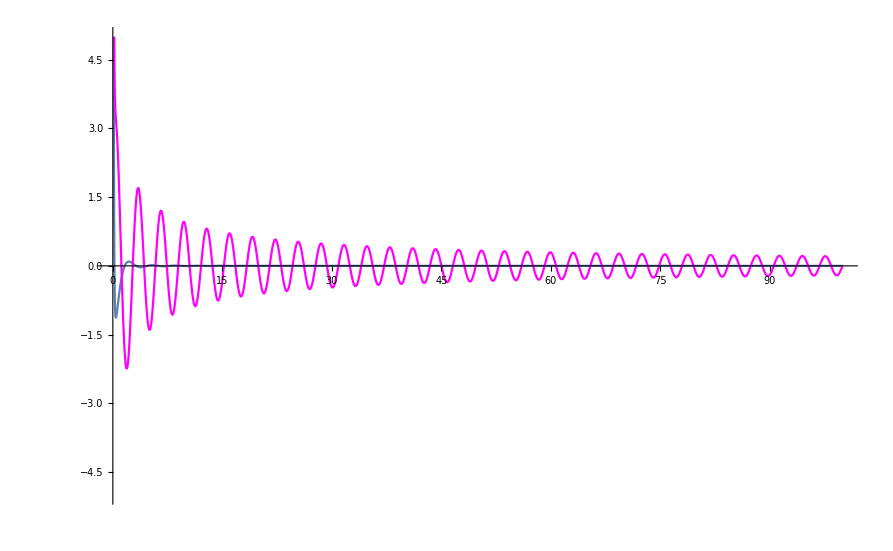

```mathematica
α =-EulerGamma+2-Log[2];
B = EulerGamma+Log[2]-(ⅈ π)/2;
Int1[x_] :=Re[ⅇ^(2ⅈ x)/x 1/8 (3 π^2-4 ⅈ π (-2+α)-4 (-2+α)^2+4 (4-ⅈ π-2 α) ExpIntegralEi[-2 ⅈ x]+32 ⅈ x HypergeometricPFQ[{1,1,1},{2,2,2},-2 ⅈ x]+8 (-2+α) Log[x]-4 Log[x] (-2 CosIntegral[2 x]+Log[x]+2 ⅈ SinIntegral[2 x])-4 Derivative[2,0,0][Hypergeometric1F1][0,1,-2 ⅈ x])];
Int2[x_]:=Re[ⅇ^(2ⅈ x)/x( (B^2/2+π^2/4+4 ⅈ x-2 ⅈ B x+B Log[x]-2 ⅈ x Log[x]+Log[x]^2/2))];
Int3[x_]:=Re[ⅇ^(2ⅈ x)/x( (B^2/2+π^2/4+B Log[x]+Log[x]^2/2))];
p1 = Plot[Int1[x],{x,0.0001,100}, PlotRange->{-5,5}];
p2 = Plot[Int2[x],{x,0.0001,100}, PlotStyle->Red, PlotRange->{-5,5}];
p3 =  Plot[Int3[x],{x,0.0001,100}, PlotStyle->Magenta, PlotRange->{-5,5}];
Show[p1,p2,p3]
```

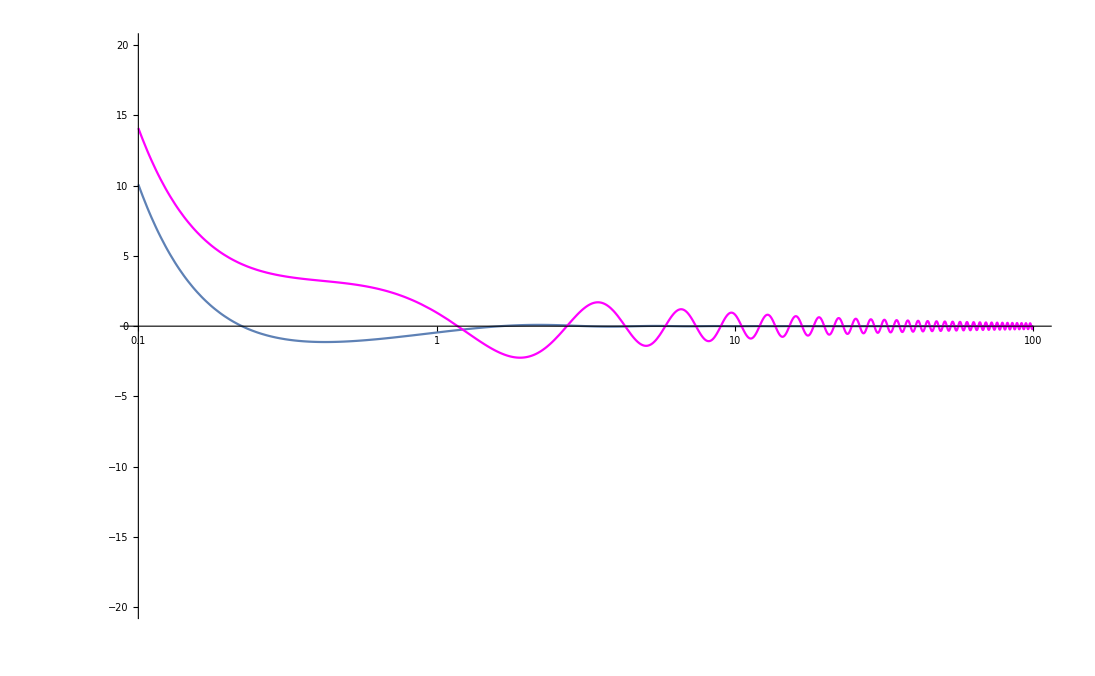

```mathematica
p11 = LogLinearPlot[Int1[x],{x,0.1,100}, PlotRange->{-20,20}];
p22 =LogLinearPlot[Int2[x],{x,0.1,100}, PlotStyle->Red, PlotRange->{-20,20}];
p33 =  LogLinearPlot[Int3[x],{x,0.1,100}, PlotStyle->Magenta, PlotRange->{-20,20}];
Show[p11,p22,p33]
```

Another way to find F000:

We also recognize that ∫_x^∞ du ⅇ^(2ⅈ u)/u(B^2/2+π^2/4+B Log[u]+Log[u]^2/2) is basically (B^2/2+π^2/4) F0 + B F1 + F2/2. Then, we can ALSO find F000 using the previous results:

```mathematica
F0 = Gamma[0,-2 ⅈ x]; 
F1 = 2 ⅈ x HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ x]+1/24 (12 EulerGamma^2-12 ⅈ EulerGamma π-π^2+12 Log[2]^2+12 ⅈ π Log[x/2])+EulerGamma Log[2 x]+1/2 Log[x] (-2 ExpIntegralEi[2 ⅈ x]+Log[4 x]); 
F2 = 1/24 (-8 EulerGamma^3+ⅈ π^3-96 ⅈ x HypergeometricPFQ[{1,1,1,1},{2,2,2,2},2 ⅈ x]+12 ⅈ EulerGamma^2 (π+2 ⅈ Log[2])+12 ⅈ π Log[2]^2+2 EulerGamma (π^2+12 ⅈ π Log[2]-12 Log[2]^2)+π^2 Log[4]+4 Log[x] (24 ⅈ x HypergeometricPFQ[{1,1,1},{2,2,2},2 ⅈ x]+Log[x] (6 EulerGamma+3 ⅈ π-6 ExpIntegralEi[2 ⅈ x]+Log[64]+4 Log[x]))-8 (Log[2]^3+2 Zeta[3]));
F0lim = -B-2 ⅈ x-Log[x];
F1lim = B^2/2+π^2/12+2 ⅈ x-2 ⅈ x Log[x]-Log[x]^2/2; 
F2lim = -B^3/3-(B π^2)/6-4 ⅈ x+4 ⅈ x Log[x]-2 ⅈ x Log[x]^2-Log[x]^3/3-(2 Zeta[3])/3;
```

Then

```mathematica
FullSimplify[(B^2/2+π^2/4) ( -B-2 ⅈ x-Log[x]) + B( B^2/2+π^2/12+2 ⅈ x-2 ⅈ x Log[x]-Log[x]^2/2)+1/2 (-B^3/3-(B π^2)/6-4 ⅈ x+4 ⅈ x Log[x]-2 ⅈ x Log[x]^2-Log[x]^3/3-(2 Zeta[3])/3), Assumptions-> x>0 ]//Expand
```

-B^3/6-(B π^2)/4-2 ⅈ x+2 ⅈ B x-ⅈ B^2 x-1/2 ⅈ π^2 x-1/2 B^2 Log[x]-1/4 π^2 Log[x]+2 ⅈ x Log[x]-2 ⅈ B x Log[x]-1/2 B Log[x]^2-ⅈ x Log[x]^2-Log[x]^3/6-Zeta[3]/3

```mathematica
FullSimplify[(-B^3/6-(B π^2)/4-1/2 B^2 Log[x]-1/4 π^2 Log[x]-1/2 B Log[x]^2-Log[x]^3/6-Zeta[3]/3) /. B-> -α-(ⅈ π)/2+2 ]//Expand
```

-4/3+ⅈ π-π^2/4+(5 ⅈ π^3)/48+2 α-ⅈ π α+(π^2 α)/8-α^2+1/4 ⅈ π α^2+α^3/6-2 Log[x]+ⅈ π Log[x]-1/8 π^2 Log[x]+2 α Log[x]-1/2 ⅈ π α Log[x]-1/2 α^2 Log[x]-Log[x]^2+1/4 ⅈ π Log[x]^2+1/2 α Log[x]^2-Log[x]^3/6-Zeta[3]/3